```mathematica
(* ================*)(*0) Project setup and load exported result tables*)(* ==============================*)

projRoot=DirectoryName[NotebookDirectory[]];

outDir=FileNameJoin[{projRoot,"output"}];
figDir=FileNameJoin[{outDir,"figures"}];
tabDir=FileNameJoin[{outDir,"tables"}];

If[!DirectoryQ[figDir],CreateDirectory[figDir]];

ClearAll[importCSVAsDataset];

importCSVAsDataset[file_String]:=Module[{raw,header,rows},raw=Import[file,"CSV"];
header=First[raw];
rows=Rest[raw];
Dataset[AssociationThread[header,#]&/@rows]];

(*Main experiment datasets*)

pcFile=FileNameJoin[{tabDir,"main_pc_long.csv"}];

opFile=FileNameJoin[{tabDir,"main_op_long.csv"}];

icFile=FileNameJoin[{tabDir,"main_ic_long.csv"}];

mallowsFile=FileNameJoin[{tabDir,"main_mallows_long.csv"}];

gapMainFile=FileNameJoin[{tabDir,"main_gap_long.csv"}];

mallowsCentralFile=FileNameJoin[{tabDir,"mallows_central_support_long.csv"}];

(*Parameter-sweep datasets*)

ceCompromiseFile=FileNameJoin[{tabDir,"op_ce_compromise_sweep_long.csv"}];

fig5SweepFile=FileNameJoin[{tabDir,"op_midscore_parameter_sweep_long.csv"}];

requiredFiles={pcFile,opFile,icFile,mallowsFile,mallowsCentralFile,gapMainFile,ceCompromiseFile,fig5SweepFile};

If[!And@@(FileExistsQ/@requiredFiles),Print["ERROR: One or more required CSV files are missing."];
Print/@Select[requiredFiles,!FileExistsQ[#]&];
Abort[];];

dsPC=importCSVAsDataset[pcFile];
dsOP=importCSVAsDataset[opFile];
dsIC=importCSVAsDataset[icFile];
dsMallows=importCSVAsDataset[mallowsFile];
dsGapMain=importCSVAsDataset[gapMainFile];

dsMallowsCentral=importCSVAsDataset[mallowsCentralFile];

dsCECompromise=importCSVAsDataset[ceCompromiseFile];

dsFig5=importCSVAsDataset[fig5SweepFile];

Print["Loaded all result datasets OK."];
```

Loaded all result datasets OK.

```mathematica
(* =====================*)(*1) Common helpers and plot styles*)(* =========================*)

ClearAll[rowsOf,metricRows,makeSeries,ruleOrder,ruleStyles,lambdaStyles,lambdaLabels];

(*Work with Dataset or a list of Associations*)
rowsOf[ds_Dataset]:=Normal[ds];
rowsOf[x_List]:=x;

(*Select one metric,optionally one rule*)
metricRows[ds_,metric_String,rule_:All]:=Module[{rows=rowsOf[ds]},Select[rows,(#["Metric"]===metric&&(rule===All||#["Rule"]===rule))&]];

(*Build sorted {x,value} series for one rule and one metric*)
makeSeries[ds_,metric_String,rule_String,xKey_String,extraCondition_:(True&)]:=Module[{rows},rows=Select[metricRows[ds,metric,rule],NumericQ[#["Value"]]&&NumericQ[#[xKey]]&&TrueQ[extraCondition[#]]&];
SortBy[({N[#[xKey]],N[#["Value"]]}&)/@rows,First]];

(*------------------------------------------------------------*)
(*Rule order and grayscale styles*)
(*------------------------------------------------------------*)

ruleOrder={"Borda","Coombs","Fallback","Plurality","QR","SDM"};

ruleStyles=<|"Borda"->Directive[GrayLevel[0.15],AbsoluteThickness[1.8]],"Coombs"->Directive[GrayLevel[0.35],AbsoluteThickness[1.8],Dashing[{0.03,0.015}]],"Fallback"->Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dashing[{0.01,0.01}]],"Plurality"->Directive[GrayLevel[0.05],AbsoluteThickness[2.0]],"QR"->Directive[GrayLevel[0.30],AbsoluteThickness[2.2],Dashing[{0.06,0.015}]],"SDM"->Directive[GrayLevel[0.65],AbsoluteThickness[2.2],Dashing[{0.025,0.012}]]|>;

(*------------------------------------------------------------*)
(*Styles for lambda trajectories in CE-compromise figures*)
(*------------------------------------------------------------*)

lambdaPlotValues={0.2,0.5,0.8,1.0};

lambdaGrays=AssociationThread[lambdaPlotValues->Subdivide[0.75,0.10,Length[lambdaPlotValues]-1]];

lambdaStyles=Association@Table[lam->Directive[GrayLevel[lambdaGrays[lam]],AbsoluteThickness[2.0]],{lam,lambdaPlotValues}];

lambdaLabels=Association@Table[lam->("λ = "<>ToString@NumberForm[lam,{2,1}]),{lam,lambdaPlotValues}];

Print["Common plotting helpers and styles loaded."];
```

Common plotting helpers and styles loaded.

```mathematica
(* =====================*)(*2) Prepare Figure 1 data:IC Gap and MidScore*)(* ======================*)

Print["Preparing Figure 1 data..."];

fig1Rules=ruleOrder;
fig1MValues={3,5,7,10};

(*------------------------------------------------------------*)
(*Panel (a):Compromise Gap*)
(*Correct per-profile Gap comes from dsGapMain*)
(*------------------------------------------------------------*)

fig1GapSeries=Association@Table[rule->makeSeries[dsGapMain,"Gap",rule,"m",(#["Model"]==="IC"&)],{rule,fig1Rules}];

(*------------------------------------------------------------*)
(*Panel (b):MidScore*)
(*------------------------------------------------------------*)

fig1MidSeries=Association@Table[rule->makeSeries[dsIC,"MidScore",rule,"m"],{rule,fig1Rules}];

(*------------------------------------------------------------*)
(*Validation*)
(*------------------------------------------------------------*)

fig1GapCheck=And@@Table[Length[fig1GapSeries[rule]]==Length[fig1MValues]&&Sort[fig1GapSeries[rule][[All,1]]]==fig1MValues,{rule,fig1Rules}];

fig1MidCheck=And@@Table[Length[fig1MidSeries[rule]]==Length[fig1MValues]&&Sort[fig1MidSeries[rule][[All,1]]]==fig1MValues,{rule,fig1Rules}];

Print["Gap series complete:      ",fig1GapCheck];
Print["MidScore series complete: ",fig1MidCheck];
Print[""];
Print["FIGURE 1 DATA OK:          ",fig1GapCheck&&fig1MidCheck];
```

Preparing Figure 1 data...

Gap series complete:      True

MidScore series complete: True

FIGURE 1 DATA OK:          True

Reproducing Figure 1...

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure1a_ic_gap.png

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure1b_ic_midscore.png

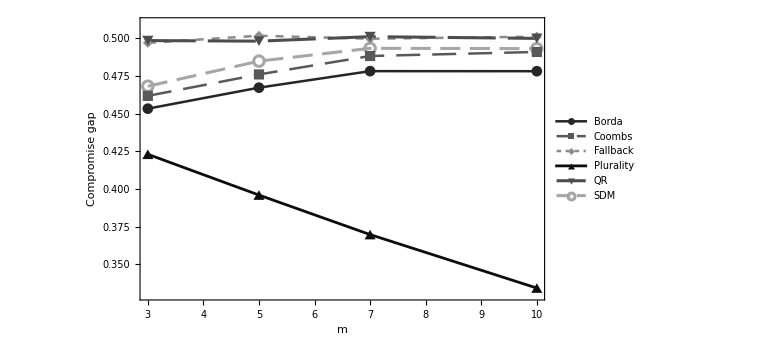

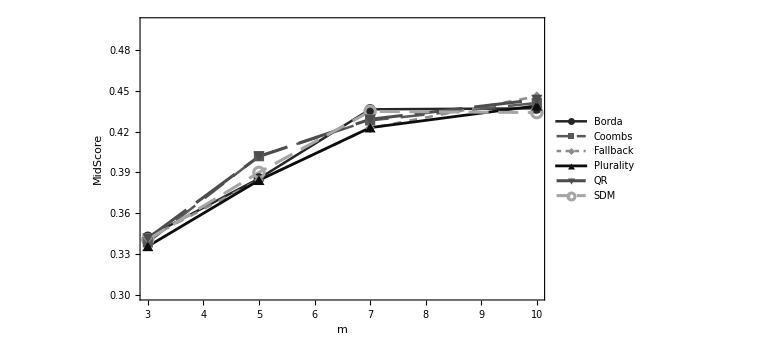

```mathematica
(* =========================*)(*3) Reproduce Figure 1*)(* ====================*)

Print["Reproducing Figure 1..."];

fig1GapPlot=ListLinePlot[Values[fig1GapSeries],PlotStyle->(ruleStyles/@fig1Rules),PlotLegends->Placed[fig1Rules,Right],Frame->True,FrameLabel->{"m","Compromise gap"},PlotRange->{{3,10},{0.33,0.51}},PlotMarkers->Automatic,ImageSize->Large];

fig1MidPlot=ListLinePlot[Values[fig1MidSeries],PlotStyle->(ruleStyles/@fig1Rules),PlotLegends->Placed[fig1Rules,Right],Frame->True,FrameLabel->{"m","MidScore"},PlotRange->{{3,10},{0.3,0.5}},PlotMarkers->Automatic,ImageSize->Large];

fig1GapFile=FileNameJoin[{figDir,"figure1a_ic_gap.png"}];

fig1MidFile=FileNameJoin[{figDir,"figure1b_ic_midscore.png"}];

Export[fig1GapFile,Rasterize[fig1GapPlot,ImageResolution->300],"PNG"];

Export[fig1MidFile,Rasterize[fig1MidPlot,ImageResolution->300],"PNG"];

Print["Saved: ",fig1GapFile];
Print["Saved: ",fig1MidFile];

fig1GapPlot
fig1MidPlot
```

Reproducing Figure 2...

Figure 2 series complete: True

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure2_mallows_central_winner.png

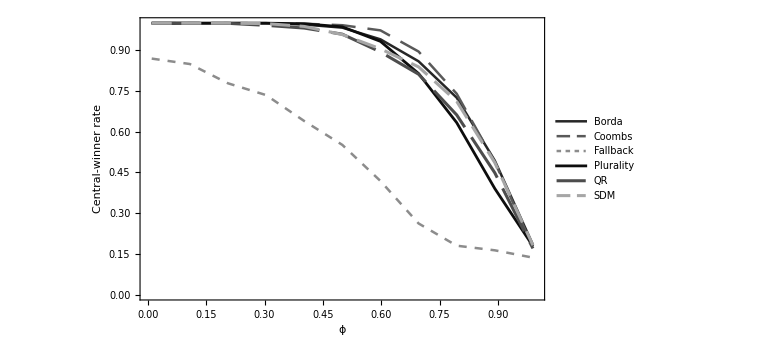

```mathematica
(* ========================*)(*4) Reproduce Figure 2:Mallows central-winner rate*)(* ====================*)

Print["Reproducing Figure 2..."];

fig2Rules=ruleOrder;
fig2M=7;

fig2Rows=Select[Normal@dsMallowsCentral,#["m"]==fig2M&];

fig2Series=Association@Table[rule->SortBy[({N[#["phi"]],N[#["CentralWinnerRate"]]}&)/@Select[fig2Rows,#["Rule"]===rule&],First],{rule,fig2Rules}];

fig2Check=And@@Table[Length[fig2Series[rule]]==11,{rule,fig2Rules}];

Print["Figure 2 series complete: ",fig2Check];

fig2Plot=ListLinePlot[Values[fig2Series],PlotStyle->(ruleStyles/@fig2Rules),PlotLegends->Placed[fig2Rules,Right],Frame->True,FrameLabel->{"ϕ","Central-winner rate"},PlotRange->{{0,1},{0,1}},ImageSize->Large];

fig2File=FileNameJoin[{figDir,"figure2_mallows_central_winner.png"}];

Export[fig2File,Rasterize[fig2Plot,ImageResolution->300],"PNG"];

Print["Saved: ",fig2File];

fig2Plot
```

```mathematica
(* ==========================*)(*5) Prepare Figure 3 data:PC Top2 and Gap*)(* ===========================*)

Print["Preparing Figure 3 data..."];

fig3Rules=ruleOrder;
fig3M=3;
fig3LambdaValues=N@Range[0,1,0.1];

(*------------------------------------------------------------*)
(*Panel (a):Top2 acceptability*)
(*------------------------------------------------------------*)

fig3Top2Series=Association@Table[rule->makeSeries[dsPC,"Top2Acceptability",rule,"lambda",(#["m"]==fig3M&)],{rule,fig3Rules}];

(*------------------------------------------------------------*)
(*Panel (b):Correct per-profile compromise Gap*)
(*------------------------------------------------------------*)

fig3GapSeries=Association@Table[rule->makeSeries[dsGapMain,"Gap",rule,"lambda",(#["Model"]==="Polarized"&&#["m"]==fig3M&)],{rule,fig3Rules}];

(*------------------------------------------------------------*)
(*Validation*)
(*------------------------------------------------------------*)

fig3Top2Check=And@@Table[Length[fig3Top2Series[rule]]==Length[fig3LambdaValues]&&Max[Abs[fig3Top2Series[rule][[All,1]]-fig3LambdaValues]]<10^-8,{rule,fig3Rules}];

fig3GapCheck=And@@Table[Length[fig3GapSeries[rule]]==Length[fig3LambdaValues]&&Max[Abs[fig3GapSeries[rule][[All,1]]-fig3LambdaValues]]<10^-8,{rule,fig3Rules}];

Print["Top2 series complete: ",fig3Top2Check];
Print["Gap series complete:  ",fig3GapCheck];
Print[""];
Print["FIGURE 3 DATA OK:      ",fig3Top2Check&&fig3GapCheck];
```

Preparing Figure 3 data...

Top2 series complete: True

Gap series complete:  True

FIGURE 3 DATA OK:      True

Reproducing Figure 3...

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure3a_pc_top2_m3.png

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure3b_pc_gap_m3.png

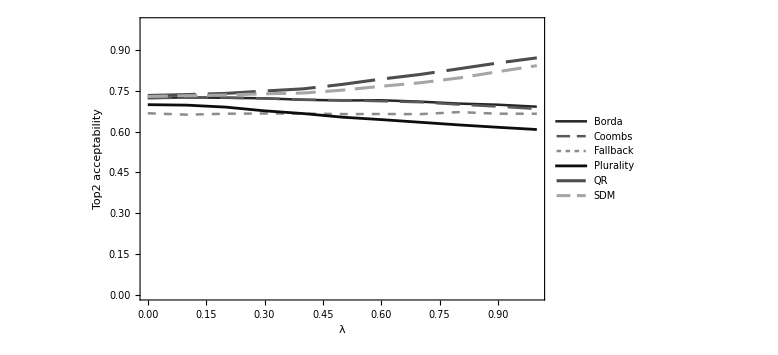

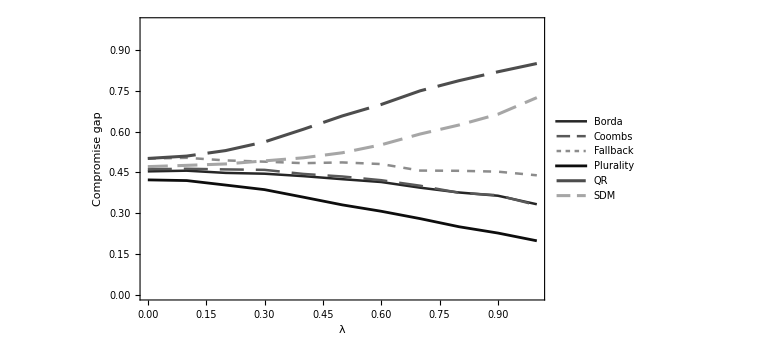

```mathematica
(* ===========================*)(*6) Reproduce Figure 3:PC Top2 acceptability and Gap*)(* =================================*)

Print["Reproducing Figure 3..."];

(*------------------------------------------------------------*)
(*Panel (a):Top2 acceptability*)
(*------------------------------------------------------------*)

fig3Top2Plot=ListLinePlot[Values[fig3Top2Series],PlotStyle->(ruleStyles/@fig3Rules),PlotLegends->Placed[fig3Rules,Right],Frame->True,FrameLabel->{"λ","Top2 acceptability"},PlotRange->{{0,1},{0,1}},ImageSize->Large];

(*------------------------------------------------------------*)
(*Panel (b):Compromise Gap*)
(*------------------------------------------------------------*)

fig3GapPlot=ListLinePlot[Values[fig3GapSeries],PlotStyle->(ruleStyles/@fig3Rules),PlotLegends->Placed[fig3Rules,Right],Frame->True,FrameLabel->{"λ","Compromise gap"},PlotRange->{{0,1},{0,1}},ImageSize->Large];

(*------------------------------------------------------------*)
(*Export*)
(*------------------------------------------------------------*)

fig3Top2File=FileNameJoin[{figDir,"figure3a_pc_top2_m3.png"}];

fig3GapFile=FileNameJoin[{figDir,"figure3b_pc_gap_m3.png"}];

Export[fig3Top2File,Rasterize[fig3Top2Plot,ImageResolution->300],"PNG"];

Export[fig3GapFile,Rasterize[fig3GapPlot,ImageResolution->300],"PNG"];

Print["Saved: ",fig3Top2File];
Print["Saved: ",fig3GapFile];

fig3Top2Plot
fig3GapPlot
```

```mathematica
(* ===============================*)(*7) Prepare Figure 4 data:OP MidScore for m=3 and m=10*)(* ======================*)

Print["Preparing Figure 4 data..."];

fig4Rules=ruleOrder;
fig4MValues={3,10};
fig4LambdaValues=N@Range[0,1,0.1];

fig4Series=Association@Table[m->Association@Table[rule->makeSeries[dsOP,"MidScore",rule,"lambda",(#["m"]==m&)],{rule,fig4Rules}],{m,fig4MValues}];

fig4Check=And@@Flatten@Table[Length[fig4Series[m][rule]]==Length[fig4LambdaValues]&&Max[Abs[fig4Series[m][rule][[All,1]]-fig4LambdaValues]]<10^-8,{m,fig4MValues},{rule,fig4Rules}];

Print["Figure 4 series complete: ",fig4Check];
Print[""];
Print["FIGURE 4 DATA OK:          ",fig4Check];
```

Preparing Figure 4 data...

Figure 4 series complete: True

FIGURE 4 DATA OK:          True

Reproducing Figure 4...

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure4a_op_midscore_m3.png

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure4b_op_midscore_m10.png

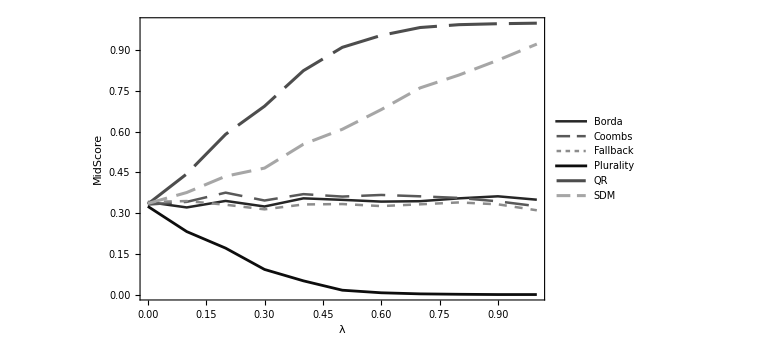

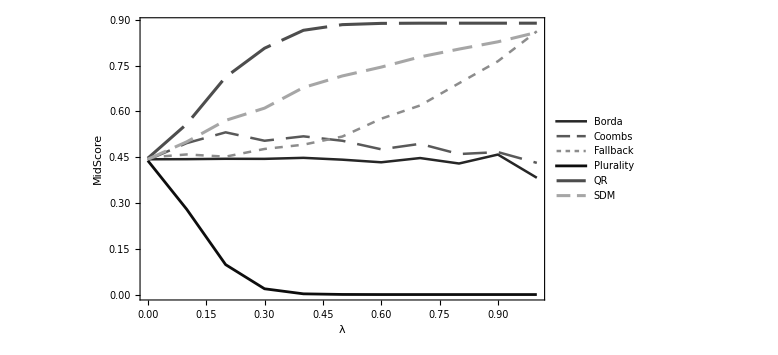

```mathematica
(* =================================*)(*8) Reproduce Figure 4:OP MidScore*)(* ==============================*)

Print["Reproducing Figure 4..."];

(*------------------------------------------------------------*)
(*Panel (a):m=3*)
(*------------------------------------------------------------*)

fig4M3Plot=ListLinePlot[Values[fig4Series[3]],PlotStyle->(ruleStyles/@fig4Rules),PlotLegends->Placed[fig4Rules,Right],Frame->True,FrameLabel->{"λ","MidScore"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*Panel (b):m=10*)
(*------------------------------------------------------------*)

fig4M10Plot=ListLinePlot[Values[fig4Series[10]],PlotStyle->(ruleStyles/@fig4Rules),PlotLegends->Placed[fig4Rules,Right],Frame->True,FrameLabel->{"λ","MidScore"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*Export*)
(*------------------------------------------------------------*)

fig4M3File=FileNameJoin[{figDir,"figure4a_op_midscore_m3.png"}];

fig4M10File=FileNameJoin[{figDir,"figure4b_op_midscore_m10.png"}];

Export[fig4M3File,Rasterize[fig4M3Plot,ImageResolution->300],"PNG"];

Export[fig4M10File,Rasterize[fig4M10Plot,ImageResolution->300],"PNG"];

Print["Saved: ",fig4M3File];
Print["Saved: ",fig4M10File];

fig4M3Plot
fig4M10Plot
```

```mathematica
(* ========================*)(*9) Prepare Figure 5 data:OP MidScore parameter sweep*)(* ======================*)

Print["Preparing Figure 5 data..."];

fig5LambdaValues=N@Range[0,1,0.1];

fig5QValues=N@{0.55,2/3,0.80,0.95};

fig5PValues=N@{1.15200309344505,Log[3]/Log[2],2.32192809488736,4.32192809488736};

(*------------------------------------------------------------*)
(*QR series:one curve for each q*)
(*------------------------------------------------------------*)

fig5QRSeries=Association@Table[q->SortBy[({N[#["lambda"]],N[#["Value"]]}&)/@Select[Normal@dsFig5,#["Rule"]==="QR"&&#["Metric"]==="MidScore"&&Abs[N[#["q"]]-q]<10^-8&],First],{q,fig5QValues}];

(*------------------------------------------------------------*)
(*SDM series:one curve for each p*)
(*------------------------------------------------------------*)

fig5SDMSeries=Association@Table[p->SortBy[({N[#["lambda"]],N[#["Value"]]}&)/@Select[Normal@dsFig5,#["Rule"]==="SDM"&&#["Metric"]==="MidScore"&&Abs[N[#["p"]]-p]<10^-8&],First],{p,fig5PValues}];

(*------------------------------------------------------------*)
(*Validation*)
(*------------------------------------------------------------*)

fig5QRCheck=And@@Table[Length[fig5QRSeries[q]]==Length[fig5LambdaValues]&&Max[Abs[fig5QRSeries[q][[All,1]]-fig5LambdaValues]]<10^-8,{q,fig5QValues}];

fig5SDMCheck=And@@Table[Length[fig5SDMSeries[p]]==Length[fig5LambdaValues]&&Max[Abs[fig5SDMSeries[p][[All,1]]-fig5LambdaValues]]<10^-8,{p,fig5PValues}];

Print["QR series complete:  ",fig5QRCheck];
Print["SDM series complete: ",fig5SDMCheck];
Print[""];
Print["FIGURE 5 DATA OK:    ",fig5QRCheck&&fig5SDMCheck];
```

Preparing Figure 5 data...

QR series complete:  True

SDM series complete: True

FIGURE 5 DATA OK:    True

Reproducing Figure 5...

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure5a_qr_midscore_sweep.png

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure5b_sdm_midscore_sweep.png

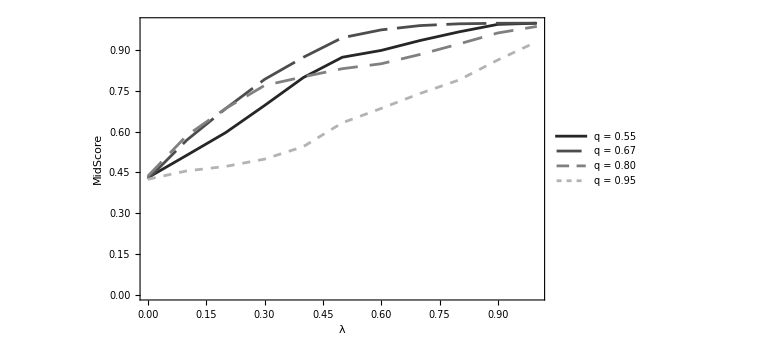

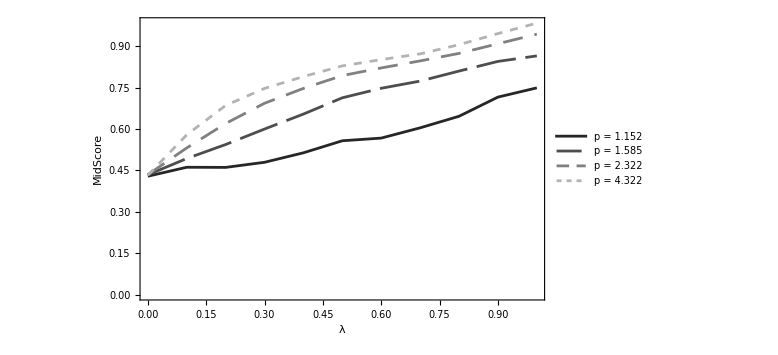

```mathematica
(* ==============================*)(*10) Reproduce Figure 5:OP MidScore parameter sweep*)(* =========================*)

Print["Reproducing Figure 5..."];

(*Distinct grayscale/dashing styles for the four parameter values*)
fig5Styles={Directive[GrayLevel[0.15],AbsoluteThickness[2.0]],Directive[GrayLevel[0.30],AbsoluteThickness[2.0],Dashing[{0.05,0.012}]],Directive[GrayLevel[0.50],AbsoluteThickness[2.0],Dashing[{0.025,0.015}]],Directive[GrayLevel[0.70],AbsoluteThickness[2.0],Dashing[{0.01,0.01}]]};

fig5QRLabels=("q = "<>ToString@NumberForm[#,{2,2}])&/@fig5QValues;

fig5SDMLabels=("p = "<>ToString@NumberForm[#,{4,3}])&/@fig5PValues;

(*------------------------------------------------------------*)
(*Panel (a):QR*)
(*------------------------------------------------------------*)

fig5QRPlot=ListLinePlot[Values[fig5QRSeries],PlotStyle->fig5Styles,PlotLegends->Placed[fig5QRLabels,Right],Frame->True,FrameLabel->{"λ","MidScore"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*Panel (b):SDM*)
(*------------------------------------------------------------*)

fig5SDMPlot=ListLinePlot[Values[fig5SDMSeries],PlotStyle->fig5Styles,PlotLegends->Placed[fig5SDMLabels,Right],Frame->True,FrameLabel->{"λ","MidScore"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*Export*)
(*------------------------------------------------------------*)

fig5QRFile=FileNameJoin[{figDir,"figure5a_qr_midscore_sweep.png"}];

fig5SDMFile=FileNameJoin[{figDir,"figure5b_sdm_midscore_sweep.png"}];

Export[fig5QRFile,Rasterize[fig5QRPlot,ImageResolution->300],"PNG"];

Export[fig5SDMFile,Rasterize[fig5SDMPlot,ImageResolution->300],"PNG"];

Print["Saved: ",fig5QRFile];
Print["Saved: ",fig5SDMFile];

fig5QRPlot
fig5SDMPlot
```

```mathematica
(* =============================*)(*11) Prepare Figure 6 data:Condorcet efficiency,PC and OP*)(* ==========================*)

Print["Preparing Figure 6 data..."];

fig6Rules=ruleOrder;
fig6M=3;
fig6LambdaValues=N@Range[0,1,0.1];

(*------------------------------------------------------------*)
(*Panel (a):Polarized Candidates*)
(*------------------------------------------------------------*)

fig6PCSeries=Association@Table[rule->makeSeries[dsPC,"CondorcetEfficiency",rule,"lambda",(#["m"]==fig6M&)],{rule,fig6Rules}];

(*------------------------------------------------------------*)
(*Panel (b):Opposite Preferences*)
(*------------------------------------------------------------*)

fig6OPSeries=Association@Table[rule->makeSeries[dsOP,"CondorcetEfficiency",rule,"lambda",(#["m"]==fig6M&)],{rule,fig6Rules}];

(*------------------------------------------------------------*)
(*Validation*)
(*------------------------------------------------------------*)

fig6PCCheck=And@@Table[Length[fig6PCSeries[rule]]==Length[fig6LambdaValues]&&Max[Abs[fig6PCSeries[rule][[All,1]]-fig6LambdaValues]]<10^-8,{rule,fig6Rules}];

fig6OPCheck=And@@Table[Length[fig6OPSeries[rule]]==Length[fig6LambdaValues]&&Max[Abs[fig6OPSeries[rule][[All,1]]-fig6LambdaValues]]<10^-8,{rule,fig6Rules}];

Print["PC series complete: ",fig6PCCheck];
Print["OP series complete: ",fig6OPCheck];
Print[""];
Print["FIGURE 6 DATA OK:    ",fig6PCCheck&&fig6OPCheck];
```

Preparing Figure 6 data...

PC series complete: True

OP series complete: True

FIGURE 6 DATA OK:    True

Reproducing Figure 6...

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure6a_pc_condorcet_efficiency_m3.png

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure6b_op_condorcet_efficiency_m3.png

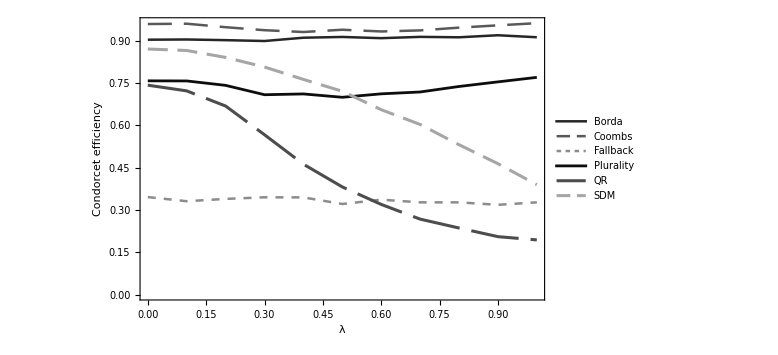

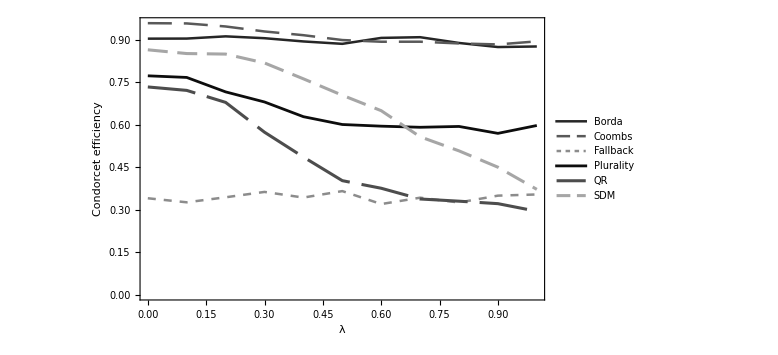

```mathematica
(* =====================================*)(*12) Reproduce Figure 6:Condorcet efficiency,PC and OP*)(* ================================*)

Print["Reproducing Figure 6..."];

(*------------------------------------------------------------*)
(*Panel (a):Polarized Candidates*)
(*------------------------------------------------------------*)

fig6PCPlot=ListLinePlot[Values[fig6PCSeries],PlotStyle->(ruleStyles/@fig6Rules),PlotLegends->Placed[fig6Rules,Right],Frame->True,FrameLabel->{"λ","Condorcet efficiency"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*Panel (b):Opposite Preferences*)
(*------------------------------------------------------------*)

fig6OPPlot=ListLinePlot[Values[fig6OPSeries],PlotStyle->(ruleStyles/@fig6Rules),PlotLegends->Placed[fig6Rules,Right],Frame->True,FrameLabel->{"λ","Condorcet efficiency"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*Export*)
(*------------------------------------------------------------*)

fig6PCFile=FileNameJoin[{figDir,"figure6a_pc_condorcet_efficiency_m3.png"}];

fig6OPFile=FileNameJoin[{figDir,"figure6b_op_condorcet_efficiency_m3.png"}];

Export[fig6PCFile,Rasterize[fig6PCPlot,ImageResolution->300],"PNG"];

Export[fig6OPFile,Rasterize[fig6OPPlot,ImageResolution->300],"PNG"];

Print["Saved: ",fig6PCFile];
Print["Saved: ",fig6OPFile];

fig6PCPlot
fig6OPPlot
```

```mathematica
(* ==================================*)(*13) Prepare Figure 7 and Table 1 data*)(* ==================*)

Print["Preparing Figure 7 and Table 1 data..."];

lambdaFig7=N@{0.2,0.5,0.8,1.0};

pGridFig7=N@{1.10,1.25,Log[3]/Log[2],1.75,2.0,2.5,3.0,4.0};

qGridFig7=N@{0.55,0.60,2/3,0.70,0.75,0.80,0.85,0.90};

ceCompRows=Normal[dsCECompromise];

(*Numerical membership test*)
ClearAll[numMemberQ];

numMemberQ[x_?NumericQ,vals_List,tol_:10^-8]:=AnyTrue[vals,Abs[N[x]-N[#]]<tol&];

(*Only the two metrics needed for Figure 7/Table 1*)
fig7Rows=Select[ceCompRows,numMemberQ[#["lambda"],lambdaFig7]&&#["m"]==7&&#["n"]==51&&Abs[N[#["phi"]]-0.15]<10^-8&&MemberQ[{"CondorcetEfficiency","MidScore"},#["Metric"]]&];

fig7SDMRows=Select[fig7Rows,#["Rule"]==="SDM"&];

fig7QRRows=Select[fig7Rows,#["Rule"]==="QR"&];

(*------------------------------------------------------------*)
(*Validation*)
(*------------------------------------------------------------*)

expectedFig7RowsPerRule=Length[lambdaFig7]*8*2;

fig7SDMCountCheck=Length[fig7SDMRows]==expectedFig7RowsPerRule;

fig7QRCountCheck=Length[fig7QRRows]==expectedFig7RowsPerRule;

actualLambdaFig7=Sort[N/@DeleteDuplicates[Lookup[fig7Rows,"lambda"]]];

fig7LambdaCheck=Length[actualLambdaFig7]==Length[lambdaFig7]&&Max[Abs[actualLambdaFig7-Sort[lambdaFig7]]]<10^-8;

actualPGridFig7=Sort[N/@DeleteDuplicates[Lookup[fig7SDMRows,"p"]]];

fig7PCheck=Length[actualPGridFig7]==Length[pGridFig7]&&Max[Abs[actualPGridFig7-Sort[pGridFig7]]]<10^-8;

actualQGridFig7=Sort[N/@DeleteDuplicates[Lookup[fig7QRRows,"q"]]];

fig7QCheck=Length[actualQGridFig7]==Length[qGridFig7]&&Max[Abs[actualQGridFig7-Sort[qGridFig7]]]<10^-8;

fig7MetricCheck=Sort@DeleteDuplicates[Lookup[fig7Rows,"Metric"]]=={"CondorcetEfficiency","MidScore"};

fig7NumericCheck=And@@(NumericQ/@Lookup[fig7Rows,"Value"]);

fig7DataOK=And[fig7SDMCountCheck,fig7QRCountCheck,fig7LambdaCheck,fig7PCheck,fig7QCheck,fig7MetricCheck,fig7NumericCheck];

Print["Expected rows per rule: ",expectedFig7RowsPerRule];
Print["Actual SDM rows:        ",Length[fig7SDMRows]];
Print["Actual QR rows:         ",Length[fig7QRRows]];
Print["Lambda grid:            ",actualLambdaFig7];
Print["Lambda grid correct:    ",fig7LambdaCheck];
Print["SDM p-grid correct:     ",fig7PCheck];
Print["QR q-grid correct:      ",fig7QCheck];
Print["Metrics correct:        ",fig7MetricCheck];
Print["All values numeric:     ",fig7NumericCheck];

Print[""];
Print["FIGURE 7 / TABLE 1 DATA OK: ",fig7DataOK];
```

Preparing Figure 7 and Table 1 data...

Expected rows per rule: 64

Actual SDM rows:        64

Actual QR rows:         64

Lambda grid:            {0.2,0.5,0.8,1.}

Lambda grid correct:    True

SDM p-grid correct:     True

QR q-grid correct:      True

Metrics correct:        True

All values numeric:     True

FIGURE 7 / TABLE 1 DATA OK: True

Reproducing Figure 7...

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure7a_op_ce_midscore_sdm.png

Saved: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\figures\figure7b_op_ce_midscore_qr.png

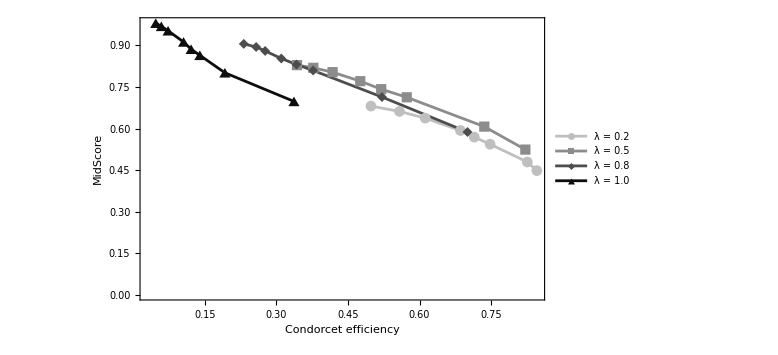

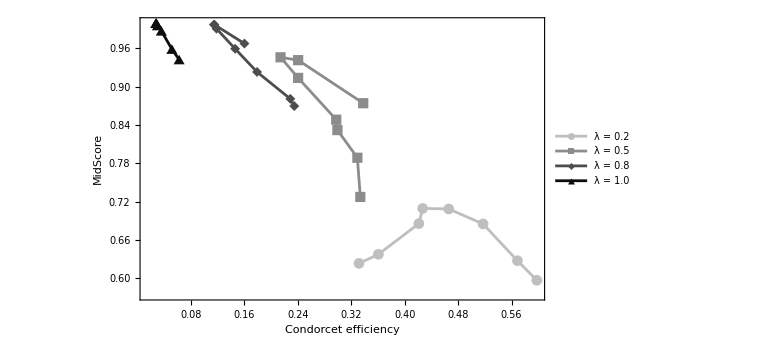

```mathematica
(* ===================*)(*14) Reproduce Figure 7:CE-MidScore parameter trajectories*)(* =========================*)

Print["Reproducing Figure 7..."];

(*------------------------------------------------------------*)
(*Build {CE,MidScore} trajectories for each lambda*)
(*------------------------------------------------------------*)

ClearAll[buildTrajectory];

buildTrajectory[rows_,rule_String,lam_?NumericQ,paramKey_String]:=Module[{sub,params,pts},sub=Select[rows,#["Rule"]===rule&&Abs[N[#["lambda"]]-N[lam]]<10^-8&];
params=Sort@DeleteDuplicates@N[Lookup[sub,paramKey]];
pts=Table[Module[{ce,mid},ce=SelectFirst[sub,Abs[N[#[paramKey]]-par]<10^-8&&#["Metric"]==="CondorcetEfficiency"&]["Value"];
mid=SelectFirst[sub,Abs[N[#[paramKey]]-par]<10^-8&&#["Metric"]==="MidScore"&]["Value"];
{N[ce],N[mid]}],{par,params}];
pts];

fig7SDMSeries=Association@Table[lam->buildTrajectory[fig7SDMRows,"SDM",lam,"p"],{lam,lambdaFig7}];

fig7QRSeries=Association@Table[lam->buildTrajectory[fig7QRRows,"QR",lam,"q"],{lam,lambdaFig7}];

(*------------------------------------------------------------*)
(*Plot styles*)
(*------------------------------------------------------------*)

fig7Styles={Directive[GrayLevel[0.75],AbsoluteThickness[2.0]],Directive[GrayLevel[0.55],AbsoluteThickness[2.0]],Directive[GrayLevel[0.30],AbsoluteThickness[2.0]],Directive[GrayLevel[0.05],AbsoluteThickness[2.0]]};

fig7Labels=("λ = "<>ToString@NumberForm[#,{2,1}])&/@lambdaFig7;

(*------------------------------------------------------------*)
(*SDM panel*)
(*------------------------------------------------------------*)

fig7SDMPlot=ListLinePlot[Values[fig7SDMSeries],PlotStyle->fig7Styles,PlotMarkers->Automatic,PlotLegends->Placed[fig7Labels,Right],Frame->True,FrameLabel->{"Condorcet efficiency","MidScore"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*QR panel*)
(*------------------------------------------------------------*)

fig7QRPlot=ListLinePlot[Values[fig7QRSeries],PlotStyle->fig7Styles,PlotMarkers->Automatic,PlotLegends->Placed[fig7Labels,Right],Frame->True,FrameLabel->{"Condorcet efficiency","MidScore"},PlotRange->All,ImageSize->Large];

(*------------------------------------------------------------*)
(*Export*)
(*------------------------------------------------------------*)

fig7SDMFile=FileNameJoin[{figDir,"figure7a_op_ce_midscore_sdm.png"}];

fig7QRFile=FileNameJoin[{figDir,"figure7b_op_ce_midscore_qr.png"}];

Export[fig7SDMFile,Rasterize[fig7SDMPlot,ImageResolution->300],"PNG"];

Export[fig7QRFile,Rasterize[fig7QRPlot,ImageResolution->300],"PNG"];

Print["Saved: ",fig7SDMFile];
Print["Saved: ",fig7QRFile];

fig7SDMPlot
fig7QRPlot
```

```mathematica
(* ===========================*)(*15) Reproduce Table 1:QR outcome dispersion*)(* =============================*)

Print["Reproducing Table 1..."];

ClearAll[qrDispersionRow];

qrDispersionRow[lam_?NumericQ]:=Module[{pts,ceVals,cVals,rc,rce,d},pts=fig7QRSeries[lam];
ceVals=pts[[All,1]];
cVals=pts[[All,2]];
rc=Max[cVals]-Min[cVals];
rce=Max[ceVals]-Min[ceVals];
d=Max[EuclideanDistance@@@Subsets[pts,{2}]];
<|"lambda"->lam,"R_C"->N[rc],"R_CE"->N[rce],"D"->N[d]|>];

table1Rows=qrDispersionRow/@lambdaFig7;

table1Dataset=Dataset[table1Rows];

Print[""];
Print["Table 1 values:"];

table1Dataset

(*------------------------------------------------------------*)
(*Comparison with values reported in the manuscript*)
(*------------------------------------------------------------*)

table1Reported={<|"lambda"->0.2,"R_C"->0.113,"R_CE"->0.256,"D"->0.257|>,<|"lambda"->0.5,"R_C"->0.219,"R_CE"->0.136,"D"->0.258|>,<|"lambda"->0.8,"R_C"->0.121,"R_CE"->0.121,"D"->0.171|>,<|"lambda"->1.0,"R_C"->0.046,"R_CE"->0.029,"D"->0.054|>};

table1Check=And@@MapThread[Abs[#1["R_C"]-#2["R_C"]]<0.0015&&Abs[#1["R_CE"]-#2["R_CE"]]<0.0015&&Abs[#1["D"]-#2["D"]]<0.0015&,{table1Rows,table1Reported}];

Print[""];
Print["TABLE 1 MATCHES MANUSCRIPT: ",table1Check];

(*------------------------------------------------------------*)
(*Export*)
(*------------------------------------------------------------*)

table1File=FileNameJoin[{tabDir,"table1_qr_dispersion.csv"}];

table1Columns={"lambda","R_C","R_CE","D"};

Export[table1File,Prepend[(Lookup[#,table1Columns]&)/@table1Rows,table1Columns],"CSV"];

Print["Saved CSV: ",table1File];
```

Reproducing Table 1...

Table 1 values:

TABLE 1 MATCHES MANUSCRIPT: False

Saved CSV: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\konferencije\2026\GDN 2026\GitHub\gdn-compromise-condorcet\output\tables\table1_qr_dispersion.csv